## dSph J factor

draco

## constant

```mathematica
G=6.67408 10^-11;(*m3 kg-1 s-2*)
DD=76*3.086 10^19;(*kpc -> m*)
Rh=0.221 3.086 10^19;(*kpc -> m*)
σlos=10.1;(*km s-1 -> m s-1*)
γ=1.0;
c=299792458;(*m s-1*)
dN=8.6 10^-11;(*GeV-3*)
σv=3 10^-26;(*cm3 s-1*)
```

## J factor

```mathematica
P[γ_]:=2/π^(1/2)((3-γ)^2 Gamma[γ-1/2])/((3-2γ)Gamma[γ]);
JSphCusp[θ_,γ_,DD_,Rh_,σlos_]:=(25*(σlos*10^3)^4)/(64 G^2)1/((DD*3.086 10^19)^2 (Rh*3.086 10^19))((DD θ*π/180)/Rh)^(3-2γ)*P[γ]*c^4*1/((1.602 10^-10)^2) 10^-10;(*GeV2 cm-5*)
```

```mathematica
JNFWCusp[θ_,DD_,Rh_,σlos_]:=25/(8 G^2)(σlos*10^3)^4(θ*π/180)/((DD*3.086 10^19) (Rh*3.086 10^19)^2)*c^4*1/((1.602 10^-10)^2) 10^-10;(*GeV2 cm-5*)
```

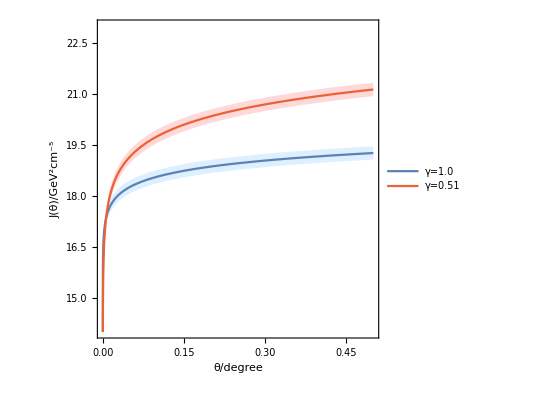

```mathematica
Plot[{Log10[JSphCusp[th,1,76,0.221,σlos]],Log10[JSphCusp[th,1,76+6,0.221+0.019,σlos-0.5]],Log10[JSphCusp[th,1,76-6,0.221-0.019,σlos+0.5]],Log10[JSphCusp[th,0.51,76,0.221,σlos]],Log10[JSphCusp[th,0.51,76+6,0.221+0.019,σlos-0.5]],Log10[JSphCusp[th,0.51,76-6,0.221-0.019,σlos+0.5]],Log10[JNFWCusp[th,76,0.221]]},{th,0,0.5},
Frame->True,FrameLabel->{"θ/degree","J(θ)/GeV^2cm^-5"},FrameStyle->FontName->"Arial",Filling->{2->{{3},{LightBlue,White}},5->{{6},{LightRed,Red}}},PlotRange->{14,23},PlotStyle->{True,None,None,True,None,None,None},PlotLegends->{"γ=1.0",None,None,"γ=0.51",None,None,None},AspectRatio->1]
```

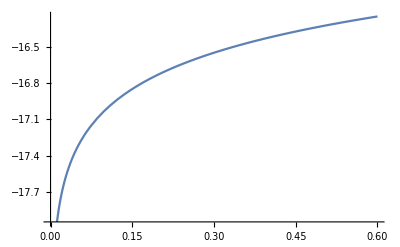

```mathematica
Plot[Log10[JSphCusp[th,1,76,0.221,σlos]*dN*σv],{th,0,0.6}]
```